Continuous Random Variables

Definite integrals

```mathematica
Integrate[1/(x-1)^3,{x,2,4}]
```

4/9

Decimal approximation:

```mathematica
NIntegrate[Log[x]Exp[-x^2],{x,1,∞}]
```

0.0358827

Solving for an unknown terminal:

```mathematica
Assuming[a>2,Solve[Integrate[2/3(x^2-1)^(3/2),{x,2,a}]==4,a,Reals]]//N
```

{{a→2.63833}}

Defining a piece-wise (hybrid) function

```mathematica
f[x_]:=Piecewise[{{x^2+1,x<-1},{x-1,x≥0}}]
```

```mathematica
f[3]
```

2

```mathematica
f[-2]
```

5

Note: The value of the function outside the explicitly defined domain is automatically taken to be 0.

```mathematica
f[-0.5]
```

0

Displaying the rule:

```mathematica
DownValues[f]
```

{HoldPattern[f[x_]]:>Piecewise[{{x^2+1, x<-1}, {x-1, x≥0}}]}

Graphing :

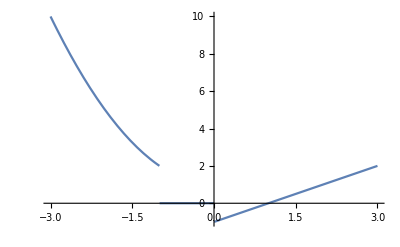

```mathematica
Plot[f[x],{x,-3,3}]
```

Restricting the domain:

```mathematica
g[x_]:=Piecewise[{{x-1,x<0},{Sqrt[x],x≥0}}]/;-3≤x≤3
```

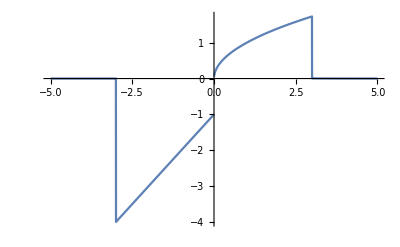

```mathematica
Plot[g[x],{x,-5,5}]
```

Calculating probability

Method 1: Use an integral.
Method 2: Define a probability distribution.

-Graphics-

Example 1:

```mathematica
Clear[f]
f[x_]:=Piecewise[{{-3/4x(x-2),0≤x≤2}}]
```

```mathematica
DownValues[f]
```

{HoldPattern[f[x_]]:>Piecewise[{{-3/4 x (x-2), 0≤x≤2}}]}

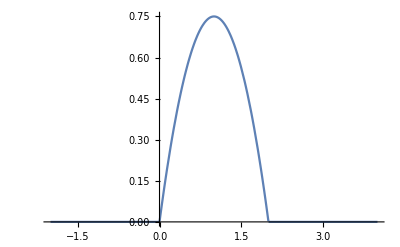

```mathematica
Plot[f[x],{x,-2,4}]
```

```mathematica
Probability[X≤1/2,X\[Distributed]ProbabilityDistribution[f[x],{x,0,2}]]
```

5/32

Note: The distributed symbol \[dist] can be entered as either \[Distributed] or Esc dist Esc

Calculating mean, variance and standard deviation
Method 1: Use integrals.
Method 2: Define a probability density function.

```mathematica
dist1=ProbabilityDistribution[f[x],{x,0,2}]
```

ProbabilityDistribution[Piecewise[{{-3/4 (-2+x) x, 0≤x≤2}, {0, True}}],{x,0,2}]

```mathematica
Probability[X≤1/2,X\[Distributed]dist1]
```

5/32

```mathematica
Probability[X≤1/2\[Conditioned]X≥1/4,X\[Distributed]dist1]
```

29/245

```mathematica
Mean[dist1]
```

1

```mathematica
StandardDeviation[dist1]
```

1/(√5)

```mathematica
Variance[dist1]
```

1/5

Inverse probability:

Example 2:

```mathematica
g[x_]:=Piecewise[{{2E^(-2x),x≥0}}]
```

Method 1:

```mathematica
Assuming[m∈Reals,Solve[Integrate[g[x],{x,-∞,m}]==1/2,m]]
```

{{m→Log[2]/2}}

Note:
The element symbol ∈ can be entered as Esc elem Esc
The reals symbol ℝcan be entered as Esc reals Esc
The infinity symbol ∞ can be entered as Esc inf Esc

Method 2:

```mathematica
Assuming[m∈Reals,Solve[Integrate[g[x],{x,m,∞}]==1/2,m]]
```

{{m→Log[2]/2}}

Method 3:

```mathematica
Assuming[m∈Reals,Solve[Integrate[g[x],{x,-∞,m}]==Integrate[g[x],{x,m,∞}],m]]
```

{{m→Log[2]/2}}

Note: Assuming[ ] is a command that lets you put a restriction on any parameters you are using in a function.
In this case, the assumption that m is real is required to tell Mathematica that the integral terminal is real.

Method 4:
Special case: median (5oth percentile).
Define a probability density function and use the Median command.

```mathematica
dist2=ProbabilityDistribution[g[x],{x,0,∞}]
```

ProbabilityDistribution[Piecewise[{{2 ⅇ^(-2 x), x≥0}, {0, True}}],{x,0,∞}]

```mathematica
Median[dist2]
```

Log[2]/2

Example 3:

```mathematica
Clear[f,x]
f[x_]:=Piecewise[{{x/16,0≤x≤4},{0.25*Exp[-0.5(x-4)],x>4}}]
```

```mathematica
DownValues[f]
```

{HoldPattern[f[x_]]:>Piecewise[{{x/16, 0≤x≤4}, {0.25 Exp[-0.5 (x-4)], x>4}}]}

Method 2:

```mathematica
Assuming[m∈Reals,Solve[Integrate[f[x],{x,m,∞}]==1/2,m]]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{m→4.}}

Check:

```mathematica
Integrate[f[x],{x,0,4}]
```

0.5

Method 4 does not work:

```mathematica
dist3=ProbabilityDistribution[f[x],{x,0,∞}]
```

ProbabilityDistribution[Piecewise[{{x/16, 0≤x≤4}, {0.25 ⅇ^(-0.5 (-4+x)), x>4}, {0, True}}],{x,0,∞}]

```mathematica
Median[dist3]
```

Median[ProbabilityDistribution[Piecewise[{{x/16, 0≤x≤4}, {0.25 ⅇ^(-0.5 (-4+x)), x>4}, {0, True}}],{x,0,∞}]]

Checking that a function is a pdf:

```mathematica
Integrate[f[x],{x,-∞,∞}]
```

1.

```mathematica
Reduce[f[x]<0,x]
```

Reduce::ratnz: Reduce was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

False

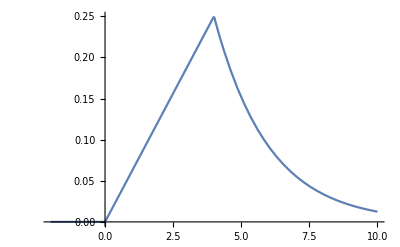

```mathematica
Plot[f[x],{x,-2,10}]
```

```mathematica
dist2=ProbabilityDistribution[f[x],{x,-∞,∞}]
```

ProbabilityDistribution[Piecewise[{{x/16, 0≤x≤4}, {0.25 ⅇ^(-0.5 (-4+x)), x>4}, {0, True}}],{x,-∞,∞}]

```mathematica
Probability[3≤X≤5,X\[Distributed]dist2]
Integrate[f[x],{x,3,5}]
```

0.415485

0.415485

```mathematica
Mean[dist2]
```

4.33333

```mathematica
StandardDeviation[dist2]
```

2.28522

```mathematica
Variance[dist2]
```

5.22222

```mathematica
Assuming[0<m<∞,Solve[Integrate[f[x],{x,0,m}]==1/2,m]]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{m→4.},{m→4.}}

Find the value of a, correct to two decimal places, such that Pr(Y ≤ a) = 0.7:

```mathematica
Assuming[0<a<∞,Solve[Integrate[f[x],{x,-∞,a}]==0.7,a]]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{a→5.02165}}

Note:

```mathematica
Clear[a]
Solve[{Integrate[f[x],{x,-∞,a}]==0.7,0<a<∞},a,Reals]
```

Integrate::pwrl: Unable to prove that integration limits {a} are real. Adding assumptions may help.

Solve::inex: Solve was unable to solve the system with inexact coefficients or the system obtained by direct rationalization of inexact numbers present in the system. Since many of the methods used by Solve require exact input, providing Solve with an exact version of the system may help.

Solve[{∫_(-∞)^a (Piecewise[{{x/16, 0≤x≤4}, {0.25 ⅇ^(-0.5 (-4+x)), x>4}, {0, True}}])ⅆx==0.7,0<a<∞},a,ℝ]